```mathematica
raw=Drop[Import[FileNameJoin[{NotebookDirectory[],"data/out.dat"}], "Table", "FieldSeparators"->{" "}, HeaderLines->1], -1];
```

```mathematica
cdata=Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]]}];
vdata=Transpose[{raw[[All, 12]], raw[[All, 13]], raw[[All, 14]]}];
pdata=raw[[All, 16]];
```

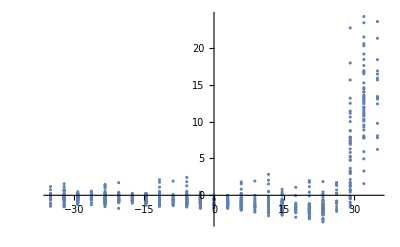

```mathematica
ListPlot[Transpose[{raw[[All, 9]], raw[[All, 12]]}], PlotRange->All]
```

```mathematica
l=Abs[Max[Flatten[cdata]]-Min[Flatten[cdata]]]
```

70.

```mathematica
vs=Max[raw[[All, 12]]]
```

24.2364

```mathematica
sw=0.04
ew=1.0
```

0.04

1.

```mathematica
slice=Select[raw,(-sw<#[[8]]/l<sw(*&&#[[9]]/l+0.5<=1*)(*&&#[[9]]/l+0.5>ew/l*))&];
```

```mathematica
vs=Max[slice[[All, 12]]]
```

17.582

```mathematica
ldd=Transpose[{slice[[All, 9]]/l+0.5, slice[[All, 12]]/vs}];
```

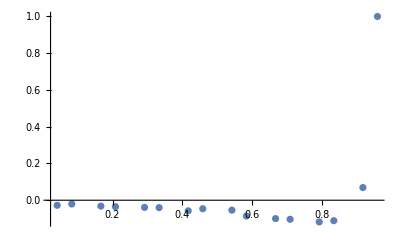

```mathematica
ldcp=ListPlot[ldd, PlotRange->All]
```

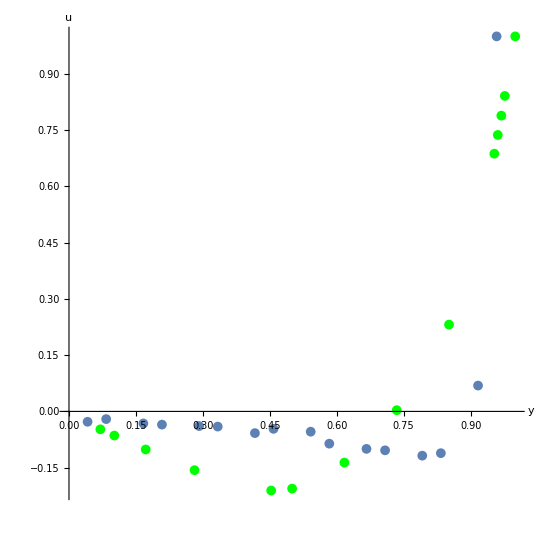

```mathematica
Show[ListPlot[{
{1, 1}, {0.9766, 0.84123}, {0.9688,0.78871}, {0.9609,0.73722}, 
{0.9531,0.68717}, {0.8516,0.23151}, {0.7344,0.00332},
 {0.6172,-0.13641}, {0.5,-0.20581},{0.4531,-0.21090}, 
{0.2813,-0.15662},{0.1719,-0.10150}, {0.1016,-0.06434}, {0.0703,-0.04775}
}, PlotStyle->Green],ldcp, AspectRatio->1, AxesLabel->{"y", "u"}]
```